```mathematica
SetDirectory["~/WorkShop/libblfq/tmc"]
```

/home/yang/WorkShop/libblfq/tmc

```mathematica
tmc=Import["tmc_stat.dat","Table"];Print[Dimensions[tmc],TableForm[tmc[[1;;5]]]];
```

{13}# | Nmax | dim | r | timing | deviation
1 | 8 | 1. | 0. | 1.6784994417006303×10^-16 | 
2 | 34 | 1. | 0. | 1.970924234037318×10^-16 | 
4 | 259 | 1. | 0. | 2.1659883715683567×10^-16 | 
8 | 3333 | 1. | 0.016 | 2.5891713721145001×10^-16 |

# dimensions

```mathematica
f12=NonlinearModelFit[Log[tmc[[2;;,{1,2}]]],a +b x + c x^2,{a,b,c},x]
```

FittedModel[1.96609+2.11804 x+0.407645 x^2]

```mathematica
f12b=NonlinearModelFit[Log[tmc[[2;;,{1,2}]]],a + b x  ,{a,b},x,Weights->tmc[[2;;,1]]]
```

FittedModel[-0.411187+4.2348 x]

```mathematica
f12c=NonlinearModelFit[tmc[[2;;,{1,2}]],a x^b  ,{a,b,c},x,Weights->tmc[[2;;,1]]]
```

FittedModel[0.0987612 x^4.77244]

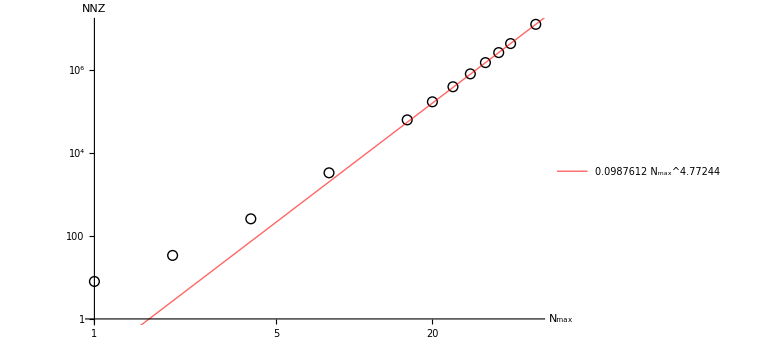

```mathematica
Show[
ListLogLogPlot[
tmc[[2;;,{1,2}]],
PlotMarkers->Graphics[{Black,Thick,Circle[]},ImageSize->10],
AxesLabel->{Subscript[N, max],NNZ},
AxesStyle->Directive[Thickness[Medium],16],
ImageSize->Large],
LogLogPlot[f12c[nmax],{nmax,1,64},
PlotRange->All,PlotStyle->{Thick,Red,Opacity[0.6]},
PlotLegends->Placed[LineLegend[{TraditionalForm[f12c[Subscript[N, max]]]},LegendMarkerSize->Large,LabelStyle->20],Scaled[{.65,.2}]]]
]
```

```mathematica
Directory[]
```

/home/yang/WorkShop/libblfq/tmc

```mathematica
Export["nnz.png",%202]
```

nnz.png

```mathematica
Export["nnz.pdf",%320]
```

nnz.pdf

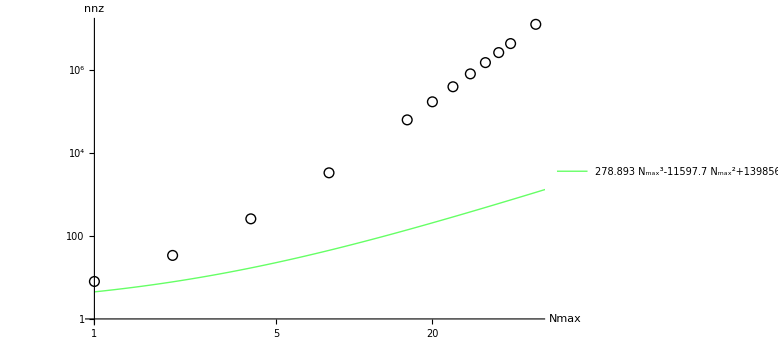

```mathematica
Show[
ListLogLogPlot[
tmc[[2;;,{1,2}]],
PlotMarkers->Graphics[{Black,Thick,Circle[]},ImageSize->10],
AxesLabel->{Nmax,nnz},
AxesStyle->Directive[Thickness[Medium],16],
ImageSize->Large],
LogLogPlot[f12[nmax],{nmax,1,64},
PlotRange->All,PlotStyle->{Thick,Green,Opacity[0.6]},
PlotLegends->Placed[LineLegend[{
TraditionalForm[f12b[Subscript[N, max]]]},LegendMarkerSize->Large,LabelStyle->20],Scaled[{.65,.2}]]]
]
```

# timing

```mathematica
f14=NonlinearModelFit[Log[tmc[[6;;,{1,4}]]],a +b x ,{a,b},x]
```

FittedModel[-25.675+8.91724 x]

```mathematica
tmc[[2;;,{1,4}]]
```

{{1,0.},{2,0.},{4,0.},{8,0.016},{16,0.476029},{20,2.73617},{24,12.7888},{28,51.2872},{32,167.746},{36,504.096},{40,1378.79},{50,12154.3}}

```mathematica
f14b=NonlinearModelFit[tmc[[4;;,{1,4}]],a x^b,{a,b},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[1.17692×10^-10 x^8.24341]

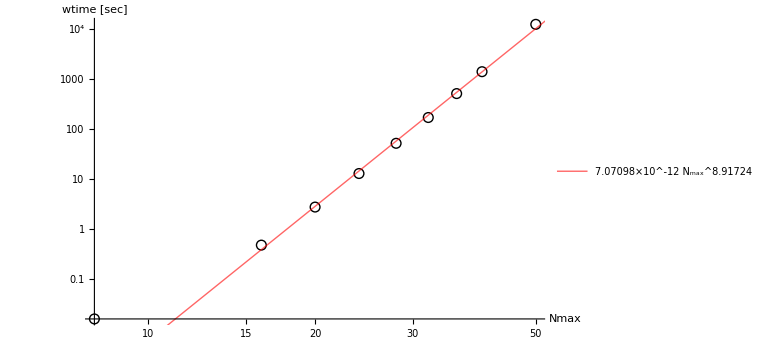

```mathematica
Show[
ListLogLogPlot[
tmc[[2;;,{1,4}]],
PlotMarkers->Graphics[{Black,Thick,EdgeForm[None],Circle[]},ImageSize->10],
AxesLabel->{Nmax,"wtime [sec]"},
AxesStyle->Directive[Thickness[Medium],16],
ImageSize->Large,
Epilog->Inset[Graphics[Text[Style["Intel Xeon E31235@3.20GHz w./ GCC",20]],ImageSize->500],Scaled[{.4,.75}]]
],
Plot[f14[lognmax],{lognmax,0,Log[64]},
PlotRange->All,PlotStyle->{Thick,Red,Opacity[0.6]},
PlotLegends->Placed[LineLegend[{
TraditionalForm[Simplify[Exp[f14[Log[Subscript[N, max]]]]]]},LegendMarkerSize->Large,LabelStyle->20],Scaled[{.4,.9}]]
]
]
```

```mathematica
Exp[f14[Log[50.]]]/3600.
```

3.94549

```mathematica
12154/3600.
```

3.37611

```mathematica
Exp[f14[Log[64.]]]/3600.
```

67.3103

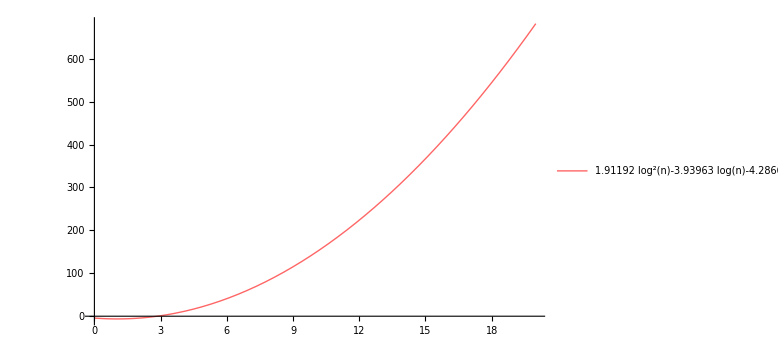

```mathematica
Plot[f14[lognmax],{lognmax,0,20},
PlotRange->All,PlotStyle->{Thick,Red,Opacity[0.6]},
PlotLegends->Placed[LineLegend[{
TraditionalForm[f14[Log[n]]]},LegendMarkerSize->Large,LabelStyle->20],Scaled[{.4,.85}]],
ImageSize->Large
]
```

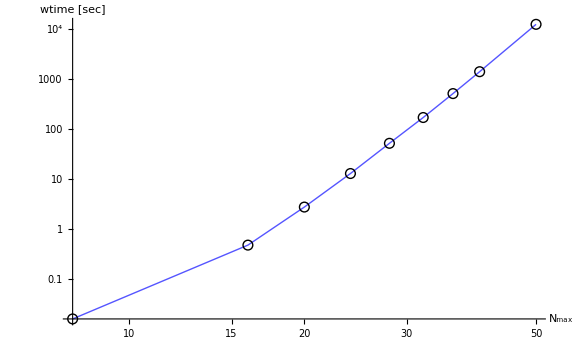

```mathematica
ListLogLogPlot[
tmc[[2;;,{1,4}]],
Joined->True,PlotStyle->Directive[Thick,Lighter@Blue],
PlotMarkers->Graphics[{Black,Thick,EdgeForm[None],Circle[]},ImageSize->10],
AxesLabel->{Subscript[N, max],"wtime [sec]"},
AxesStyle->Directive[Thickness[Medium],16],
ImageSize->Large,
Epilog->Inset[Graphics[Text[Style["Intel Xeon E31235@3.20GHz w./ GCC",20]],ImageSize->500],Scaled[{.4,.9}]]
]
```

```mathematica
Export["wtime.pdf",%330]
```

wtime.pdf

# deviation from unity

```mathematica
tmc[[5;;,{1,5}]]
```

{{8,2.5891713721145001×10^-16},{16,3.4346440253115632×10^-16},{20,8.8885482002133805×10^-16},{24,2.1743731872968834×10^-15},{28,6.1286271950355738×10^-15},{32,1.9648738420162954×10^-14},{36,5.6444400579081056×10^-14},{40,1.5547080722493025×10^-13},{50,2.6587059542292038×10^-12}}

```mathematica
f15=NonlinearModelFit[Transpose[{tmc[[6;;,1]],Log[tmc[[6;;,5]]]}],a +b x + c x^2,{a,b,c},x]
```

FittedModel[-39.2563869563810357+«59» x+«78» x^2]

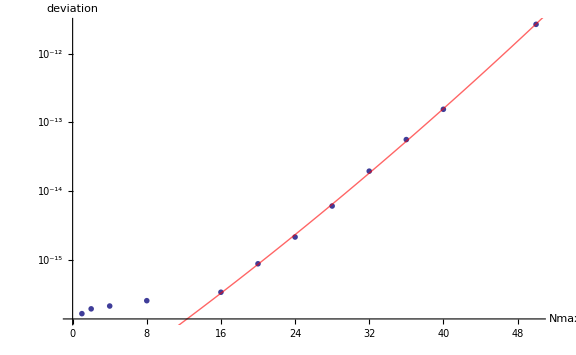

```mathematica
Show[
ListLogPlot[
tmc[[2;;,{1,5}]],
PlotMarkers->Graphics[{Black,Line[{{-1.,0},{1.,0}}],Line[{{0,-1.},{0,1.}}],Thick,Circle[{0,0}]},ImageSize->10],
AxesLabel->{Nmax,"deviation"},
AxesStyle->Directive[Thickness[Medium],16],
ImageSize->Large],
Plot[f15[nmax],{nmax,1,64},
PlotRange->All,PlotStyle->{Thick,Red,Opacity[0.6]}]
]
```

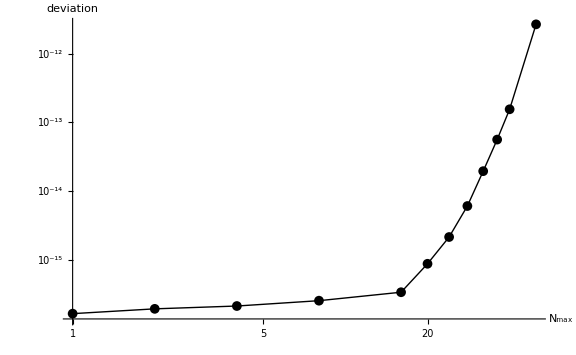

```mathematica
ListLogLogPlot[
tmc[[2;;,{1,5}]],Joined->True,
PlotMarkers->Graphics[{Black,Disk[{0,0}]},ImageSize->10],
PlotStyle->Directive[Thickness[Medium],Black],
AxesLabel->{Subscript[N, max],"deviation"},
AxesStyle->Directive[Thickness[Medium],16],
ImageSize->Large]
```

# maximum error

```mathematica
maxerr=Import["tmc_stat_omp.dat","Table"];Print[Dimensions[maxerr],TableForm[Prepend[maxerr[[2;;5]],maxerr[[1,2;;]]]]];
```

{11}Nmax | dim | ncore | r | tot_timing | wtime | stddev | maxdev
4 | 259 | 8 | 1. | 0.020000999999999998 | 0.0032959962263703346 | 2.1659883715683567×10^-16 | 4.2188474935755949×10^-15
6 | 1092 | 8 | 1. | 0.012 | 0.0017319470643997192 | 2.2507676085879381×10^-16 | 1.0769163338864018×10^-14
8 | 3333 | 8 | 1. | 0.064003999999999992 | 0.011338601820170879 | 2.5891713721145001×10^-16 | 1.4876988529977098×10^-14
12 | 17927 | 8 | 1. | 0.112007 | 0.030314620584249497 | 2.9814496996244188×10^-16 | 3.6859404417555197×10^-14

```mathematica
mx18=NonlinearModelFit[Transpose[{maxerr[[2;;,1]],Log[maxerr[[2;;,8]]]}],a +b x + c x^2,{a,b,c},x]
```

FittedModel[-34.1792604657301443+«58» x+«77» x^2]

```mathematica
mx17=NonlinearModelFit[Transpose[{maxerr[[2;;,1]],Log[maxerr[[2;;,7]]]}],a +b x + c x^2,{a,b,c},x]
```

FittedModel[-36.5515122163928481+«78» x+«78» x^2]

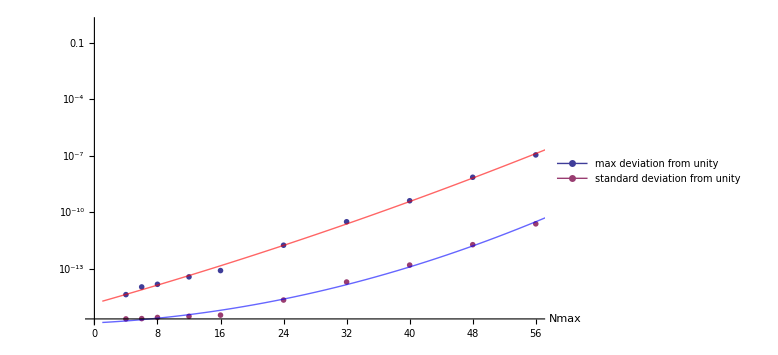

```mathematica
Show[
ListLogPlot[
{maxerr[[2;;,{1,8}]],
maxerr[[2;;,{1,7}]]},
PlotMarkers->{Graphics[{Black,Line[{{-1.1,0},{1.1,0}}],Line[{{0,-1.1},{0,1.1}}],Thick,Circle[{0,0}]},ImageSize->12],
Graphics[{Black,Line[{{-1.1,0},{1.1,0}}],Line[{{0,-1.1},{0,1.1}}],Thick,Line[{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},ImageSize->11]},
AxesLabel->{Nmax,},
AxesStyle->Directive[Thickness[Medium],16],
ImageSize->Large,
PlotLegends->Placed[PointLegend[{"max deviation from unity","standard deviation from unity"},
LegendMarkers->Automatic,Joined->True,LabelStyle->16,LegendMarkerSize->Large],Scaled[{.3,.8}]]
],
Plot[{mx18[nmax],mx17[nmax]},{nmax,1,64},
PlotRange->All,
PlotStyle->{Directive[Thick,Red,Opacity[0.6]],
{Thick,Blue,Opacity[0.6]}}]
]
```

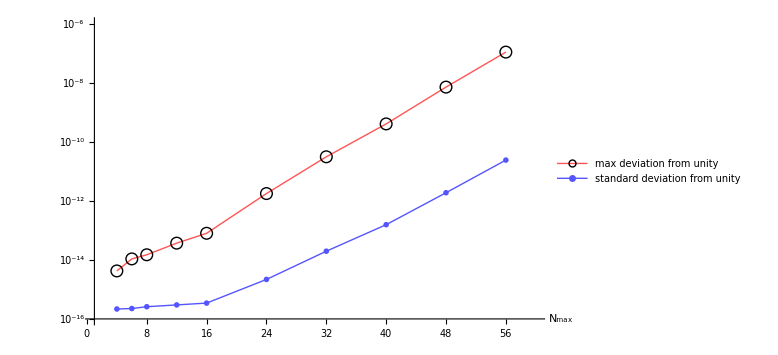

```mathematica
ListLogPlot[
{maxerr[[2;;,{1,8}]],
maxerr[[2;;,{1,7}]]},
Joined->True,
PlotRange->{{1,60},{10^-16,10^-6}},
PlotStyle->{Directive[Thick,Lighter@Red],
Directive[Thick,Lighter@Blue]},
PlotMarkers->{Graphics[{Black,Thick,Circle[{0,0}]},ImageSize->12],
Graphics[{Black,Thick,Line[{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},ImageSize->11]},
AxesLabel->{Subscript[N, max],},
AxesStyle->Directive[Thickness[Medium],16],
ImageSize->Large,
PlotLegends->Placed[PointLegend[{"max deviation from unity","standard deviation from unity"},
LegendMarkers->Automatic,Joined->True,LabelStyle->16,LegendMarkerSize->Large],Scaled[{.3,.8}]]
]
```

```mathematica
Export["deviation.pdf",%358]
```

deviation.pdf

## timing

```mathematica
fomp15=NonlinearModelFit[Log[maxerr[[5;;,{1,5}]]],a +b x ,{a,b,c},x]
```

FittedModel[-23.6581+8.41588 x]

```mathematica
fomp16=NonlinearModelFit[Log[maxerr[[5;;,{1,6}]]],a +b x ,{a,b,c},x]
```

FittedModel[-25.4427+8.64531 x]

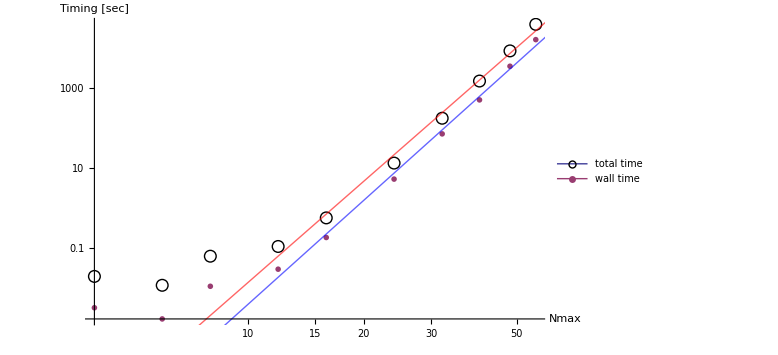

```mathematica
Show[
ListLogLogPlot[
{maxerr[[2;;,{1,5}]],
maxerr[[2;;,{1,6}]]},
PlotMarkers->{Graphics[{Black,Thick,Circle[{0,0}]},ImageSize->12],
Graphics[{Black,Thick,Line[{{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}}]},ImageSize->11]},
AxesLabel->{Nmax,"Timing [sec]"},
AxesStyle->Directive[Thickness[Medium],16],
ImageSize->Large,
PlotLegends->Placed[PointLegend[{"total time","wall time"},
LegendMarkers->Automatic,Joined->True,LabelStyle->16,LegendMarkerSize->Large],Scaled[{.3,.8}]]
],
Plot[{fomp15[x],fomp16[x]},{x,0,Log[64]},
PlotRange->All,
PlotStyle->{Directive[Thick,Red,Opacity[0.6]],
{Thick,Blue,Opacity[0.6]}}]
]
```

```mathematica
Exp[fomp15[Log[64]]]/3600.
```

23.4273

# analytic results

```mathematica
Directory[]
```

/home/yang/WorkShop/libblfq/tmc

```mathematica
<<"TalmiMoshinskyTransformation.m"
```

TODO: TalmiMoshinksy Package Welcome Information and Initialization

```mathematica
?TMC
```

TMC[N, M, n, m, n1, m1, n2, m2, x1, x2] calculates the 2D Talmi-Moshinsky coefficient without using the generalized binomial and multinomial coefficients

```mathematica
TMC[0,0,0,0,0,0,0,0,1,1]
```

1

```mathematica
enum[nmax_Integer,mj_Integer]:=
Module[{m2,n2,list,i},
i=0;
list=Reap[Do[m2=mj-m1;n2=(nmax-Abs[m1]-Abs[mj-m1])/2-n1;
If[Element[n2,Integers]&&n2>=0,
Sow[{n1,m1,n2,m2}];i++],
{m1,Floor[(mj-nmax)/2],Ceiling[(mj+nmax)/2]},
{n1,0,Floor[(nmax-Abs[m1]-Abs[mj-m1])/2]}
];i];
(*Print[list];*)
If[First[list]>0,list[[2,1]],{}]
]
```

```mathematica
enum2[nmax_Integer]:=Select[Table[{mj,enum[nmax,mj]},{mj,-nmax,nmax}],Length[#[[2]]]>0&]
```

```mathematica
check[a_List,nmax_Integer,mj_Integer]:=(2a[[1]]+Abs[a[[2]]]+2a[[3]]+Abs[a[[4]]]==nmax)&&(a[[2]]+a[[4]]==mj)
```

```mathematica
enum2[2]
```

{{-2,{{0,-2,0,0},{0,-1,0,-1},{0,0,0,-2}}},{0,{{0,-1,0,1},{0,0,1,0},{1,0,0,0},{0,1,0,-1}}},{2,{{0,0,0,2},{0,1,0,1},{0,2,0,0}}}}

```mathematica
Table[check[ v,2,#[[1]]],{v,#[[2]]}]&/@enum2[2]
```

{{True,True,True},{True,True,True,True},{True,True,True}}

```mathematica
enum2[1]
```

{{-1,{{0,-1,0,0},{0,0,0,-1}}},{1,{{0,0,0,1},{0,1,0,0}}}}

```mathematica
Table[check[ v,1,#[[1]]],{v,#[[2]]}]&/@enum2[1]
```

{{True,True},{True,True}}

```mathematica
Floor[-1.1]
```

-2

```mathematica
Ceiling[-1.5]
```

-1

```mathematica
TableForm[enum2[1]]
```

-1 | 0 | -1 | 0 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0

```mathematica
TableForm[enum2[2]]
```

-2 | 0 | -2 | 0 | 0
0 | -1 | 0 | -1
0 | 0 | 0 | -2
0 | 0 | -1 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | -1
2 | 0 | 0 | 0 | 2
0 | 1 | 0 | 1
0 | 2 | 0 | 0

```mathematica
(qho=Flatten[enum2[0][[All,2]]~Join~enum2[1][[All,2]]~Join~enum2[2][[All,2]],1])//TableForm
```

0 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | -2 | 0 | 0
0 | -1 | 0 | -1
0 | 0 | 0 | -2
0 | -1 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | -1
0 | 0 | 0 | 2
0 | 1 | 0 | 1
0 | 2 | 0 | 0

```mathematica
Table[TMC@@Flatten@{u,v,1,1},{u,qho},{v,qho}]//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 1/(√2) | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | -1/(√2) | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | -1/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 1/2 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | -1/2 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/(√2) | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0 | 1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/(√2) | 1/2

```mathematica
Integrate[Exp[x Cos[θ]]Cos[m θ],{θ,0,2Pi},Assumptions->{m∈Integers,x>0}]
```

Integrate[ⅇ^(x Cos[θ]) Cos[m θ],{θ,0,2 π},Assumptions→{m∈Integers,x>0}]